```mathematica
pp[2]:=1;
```

```mathematica
pp[1]
```

```mathematica
pps[2]:={{2}};
pps[3]:={{3}};
pps[4]:={{2,2}};
pps[5]:={{5},{3,2}};
pps[6]:={{3,3},{2,2,2}};
pps[7]:={{7},{5,2},{3,2,2}};
pps[8]:={{5,3},{3,3,2},{2,2,2,2}};
pps[9]:={{7,2},{5,2,2},{3,3,3},{3,2,2,2}};
pps[10]:={{7,3},{5,5},{5,3,2},{3,3,2,2},{2,2,2,2,2}};
pps[11]:={{11},{7,2,2},{5,3,2},{5,2,2,2},{3,3,3,2},{3,2,2,2,2}};
pps[12]:={{7,5},{7,3,2},{5,5,2},{5,3,2,2},{3,3,3,3},{3,3,2,2,2},{2,2,2,2,2,2}};
```

```mathematica
Table[Length[pps[n]],{n,2,12}]
```

{1,1,1,2,2,3,3,4,5,6,7}

```mathematica
Table[Prime[n],{n,1,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
pp[2,x_]=1;
pp[n_,p_]:=pp[n,p]=If[n<2,0,
result=0;
For[i=n,i> 1,i--,
For[j=p,j>1,j--,
If[PrimeQ[i],pp[i,p],Continue];
]
]
];result
```

0

```mathematica
pp[n_] := pp[n] = Sum[If[i == n && PrimeQ[i], 1, If[PrimeQ[i], pp[n - i], 0]], 
    {i, 2, n}];
```

```mathematica
pp[5]
```

3

```mathematica
pp[2,3]
```

1

```mathematica
pp[3,2]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of i=3.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of i>1.

```mathematica
pp[0]=0;
pp[1]=0;
pp[2]=1+pp[1]pp[1];
pp[3]=1+pp[2]pp[1];
pp[4]=pp[3]pp[1]+pp[2]pp[2];
pp[5]=1+pp[4]pp[1]+pp[3]pp[2];
pp[6]=pp[5]pp[1]+pp[4]pp[2]+pp[3]pp[3];
pp[7]=1+pp[6]pp[1]+pp[5]pp[2]+pp[4]pp[3];
pp[8]=pp[7]pp[1]+pp[6]pp[2]+pp[5]pp[3]+pp[4]pp[4];
pp[9]=pp[8]pp[1]+pp[7]pp[2]+pp[6]pp[3]+pp[5]pp[4];
pp[10]=pp[9]pp[1]+pp[8]pp[2]+pp[7]pp[3]+pp[6]pp[4]+pp[5]pp[5];
```

```mathematica
Table[pp[n],{n,1,10}]
```

{0,1,1,1,2,2,4,5,8,15}

```mathematica
pp[7]
```

4

```mathematica
oeisA000607={1,0,1,1,1,2,2,3,3,4,5,6,7,9,10,12,14,17,19,23,26,30,35,40,46,52,60,67,77,87,98,111,124,140,157,175,197,219,244,272,302,336,372,413,456,504,557,614,677,744,819,899,987,1083,1186,1298,1420,1552,1695,1850,2018,2198,2394,2605,2833,3079,3344};
```

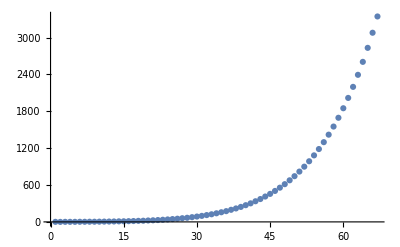

```mathematica
ListPlot[oeisA000607]
```

```mathematica
Length[oeisA000607]
```

67

```mathematica
Table[oeisA000607[[n]]-oeisA000607[[n-1]],{n,2,Length[oeisA000607]}]
```

{-1,1,0,0,1,0,1,0,1,1,1,1,2,1,2,2,3,2,4,3,4,5,5,6,6,8,7,10,10,11,13,13,16,17,18,22,22,25,28,30,34,36,41,43,48,53,57,63,67,75,80,88,96,103,112,122,132,143,155,168,180,196,211,228,246,265}

```mathematica
Last[oeisA000607]+265 7
```

5199